```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/pi/repos/HATS/testing/USSA76

```mathematica
tpr=ReadList["TPRho.tst",Number,RecordLists->True];
```

```mathematica
tpr[[1]]
tpr[[85507]]
tpr[[86007]]
```

{0.,288.15,101325.,1225.}

{85.5,187.852,0.405523,0.00752035}

{86.,186.867,0.000373383,0.00695788}

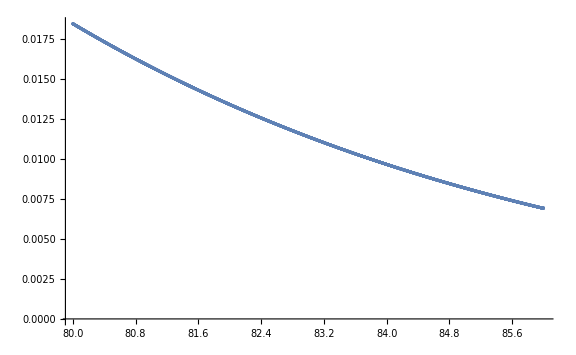

```mathematica
ListPlot[
tpr[[80007;;86007,1;;4;;3]],
ImageSize->Large]
```

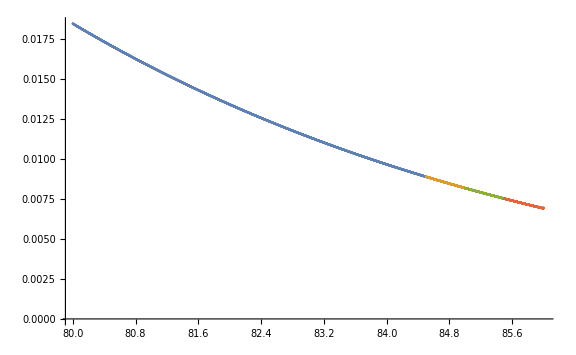

```mathematica
ListPlot[
{
tpr[[80007;;86007,1;;4;;3]],
tpr[[84507;;85007,1;;4;;3]],
tpr[[85007;;85507,1;;4;;3]],
tpr[[85507;;86007,1;;4;;3]]
},
ImageSize->Large]
```